```mathematica
path="C:\\Users\\cemh_\\Documents\\Master\\Diamonds\\master-lab-diamonds";
SetDirectory[path];

(*---------------Spectra files----------------*)

Osa001=Import[path<>"\\osa\\001.csv","CSV"]@[[34;;-1]];
Osa002=Import[path<>"\\osa\\002.csv","CSV"][[34;;-1]];
Osa003=Import[path<>"\\osa\\003.csv","CSV"][[34;;-1]];
Osa004=Import[path<>"\\osa\\004.csv","CSV"][[34;;-1]];
```

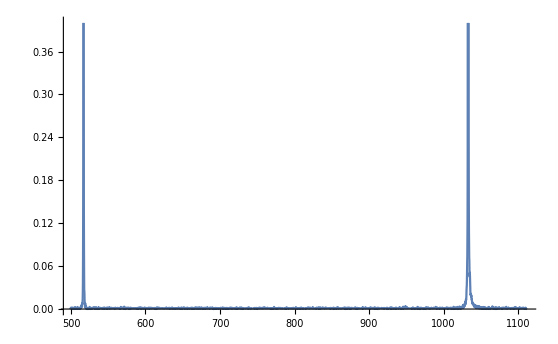

```mathematica
ListLinePlot[Table[Osa001[[x]],{x,1,Length[Osa001]-1}],PlotRange->0.4]
```

```mathematica
mstrip001=Import[path<>"\\data\\microstrip\\001.csv","CSV"][[3;;-1,{1,3}]];
mstrip002=Import[path<>"\\data\\microstrip\\002.csv","CSV"][[3;;-1,{1,3}]];
mstrip003=Import[path<>"\\data\\microstrip\\003.csv","CSV"][[3;;-1,{1,3}]];
mstrip004=Import[path<>"\\data\\microstrip\\004.csv","CSV"][[3;;-1,{1,3}]];
legend={"PS Out-In","PS In-Cpl","MS Reflection","MS transmition"};
```

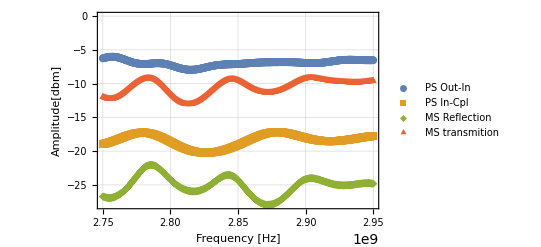

```mathematica
fig1=ListPlot[{mstrip001,mstrip002,mstrip003,mstrip004}, PlotTheme->"Detailed",PlotLegends->legend,FrameLabel->{"Frequency [Hz]","Amplitude[dbm]"}, PlotMarkers->{Automatic,8}]
Export[path<>"\\figures\\microstrip.png",fig1,"PNG"];
```

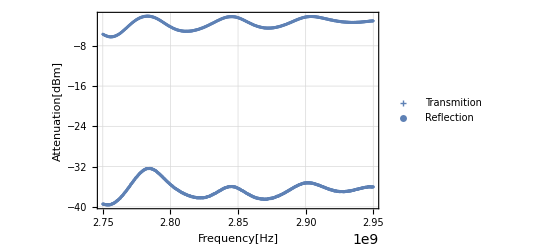

```mathematica
(*-----------------Plot trnsa and reflection-------------*)

(*

Transm= Tms-Tcpl
Reflection=Rms+Rcpl-Tcpl
*)

fig2=ListPlot[Partition[Riffle[mstrip001[[All,1]],mstrip004[[All,2]]-(mstrip001[[All,2]])],2],PlotTheme->"Detailed",FrameLabel->{"Frequency[Hz]","Attenuation[dBm]"},PlotLegends->{"Transmition"},PlotMarkers->{"+" ,3}];
fig3=ListPlot[Partition[Riffle[mstrip001[[All,1]],mstrip003[[All,2]]+mstrip002[[All,2]]-mstrip001[[All,2]]],2],PlotLegends->{"Reflection"}];
Show[fig2,fig3,PlotRange -> All]
```

0.012

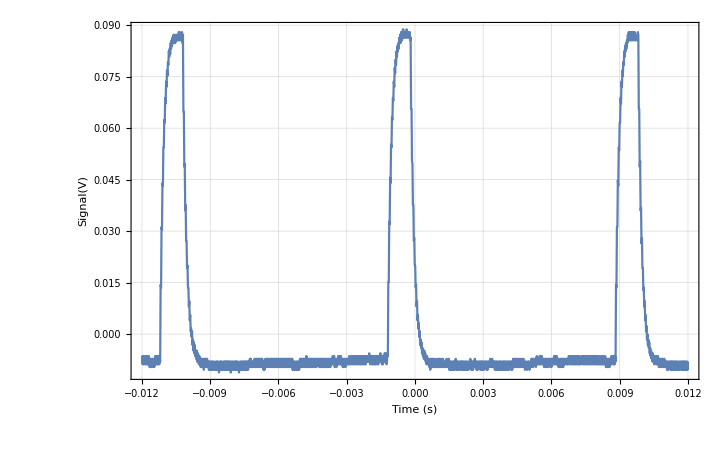

```mathematica
data=Import["C:\\Users\\cemh_\\Documents\\Master\\Diamonds\\master-lab-diamonds\\data\\osci\\apd-calibration-20mW.csv","CSV"][[2;;-1]];mmax= Max[data[[All,1]]]
fig4=ListLinePlot[data,PlotRange->All,PlotTheme->"Detailed",FrameLabel->{"Time (s)","Signal(V)"}]
```

```mathematica
S
```

FittedModel[1.13398 ⅇ^(-6046.79 x)]

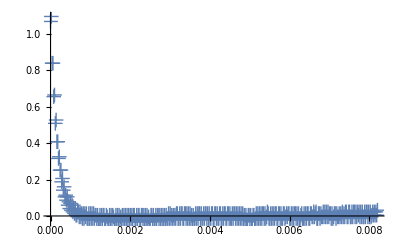

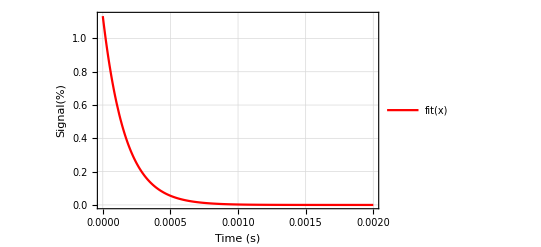

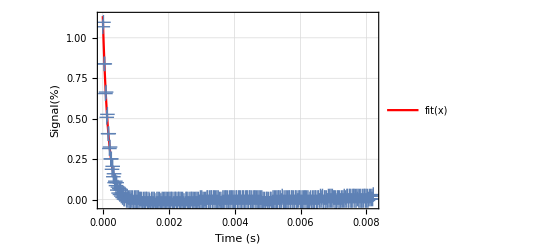

-0.000165377

```mathematica
data1=data[[90;;500]];data1[[All,2]]=(data1[[All,2]]-Mean[data[[200;;500,2]]])/Max[data1[[All,2]]];data1[[All,1]]=data1[[All,1]]-data1[[1,1]];fit=NonlinearModelFit[data1,a*Exp[(x*b)],{a,b},x,Method->"Gradient"]
dt=ListPlot[data1,PlotRange->All,PlotMarkers->{"+",15}]
f=Plot[fit[x],{x,0,0.002},PlotRange-> All,PlotStyle->{PointSize@Medium,Red},PlotTheme->"Detailed",FrameLabel->{"Time (s)","Signal(%)"}]
Show[f,dt,PlotRange-> All]
Lifetime=1/fit["BestFitParameters"][[2,2]]
```

```mathematica
%888["BasisFunctions"]
```

FittedModel::notprop: BasisFunctions is not a known property for FittedModel[1.13398 ⅇ^(-6046.79 x)]. Use FittedModel[1.13398 ⅇ^(-6046.79 x)]["Properties"] for a list of properties.

FittedModel[1.13398 ⅇ^(-6046.79 x)][BasisFunctions]

```mathematica
fit["ParameterConfidenceIntervalTable"]
tab=fit["ParameterTable"]
```

| Estimate | Standard Error | Confidence Interval
a | 1.13398 | 0.0105947 | {1.11316,1.15481}
b | -6046.79 | 84.7772 | {-6213.45,-5880.14}

| Estimate | Standard Error | t-Statistic | P-Value
a | 1.13398 | 0.0105947 | 107.033 | 3.25781×10^-301
b | -6046.79 | 84.7772 | -71.3257 | 7.32308×10^-233

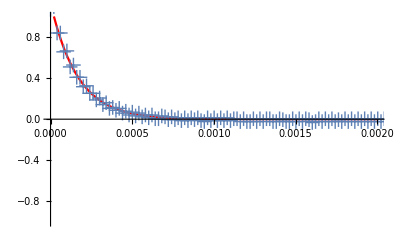

```mathematica
Show[f,dt,LegendFunction->(Column[{#,tab},Frame->True]&)]
```

```mathematica
fit
```

NonlinearModelFit::fitd: First argument data⟦90;;500⟧ in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[data⟦90;;500⟧,a ⅇ^(b x),{a,b},x,Method→Gradient]

```mathematica
N[{1/6046 , 1/84 , 1/71}]
```

{0.000165399,0.0119048,0.0140845}

```mathematica
Total[{1/6046,1/84,1/71}]
```

471547/18029172

```mathematica
N[471547/18029172]
```

0.0261547